Exercise 1.3 a)

```mathematica
Remove["Global`*"]
n = {1,2,3,4};
k := (1-√(1-h))/(1-(1-h));
m = 1- k;
myTable = {};
y[x_] :=√x;
l[x_] := k*x+m;
delta[x_] := y[x] - l[x];

dx = Solve[D[delta[x],x] == 0,x]
AppendTo[myTable, {"h","x^*","ξ"}];
Do[
    h = 10^(-i);
    AppendTo[myTable, {h, N[x /. dx], N[delta[x]/.dx]}];
    
,{i,n}]
TableForm[myTable]
```

{{x→-h^2/(4 (-2+2 √(1-h)+h))}}

h | x^* | ξ
1/10 | 0.949342 | 0.000337844
1/100 | 0.994994 | 3.14861×10^-6
1/1000 | 0.9995 | 3.12735×10^-8
1/10000 | 0.99995 | 3.12522×10^-10

{h^2/32+O[h]^3}

Exercise 1.3 b)

```mathematica
Clear[h]
derp[h_] := delta[x] /. dx
Series[derp[h], {h, 0, 2}]
Print["p: ", 2, ", c: ", 1/32]
```

{h^2/32+O[h]^3}

p: 2, c: 1/32

Exercise 2.1

{1,2,3,4,5}

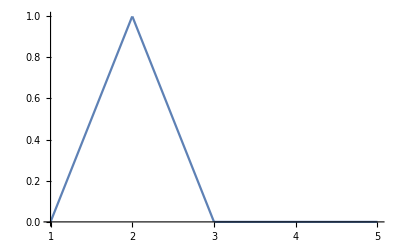

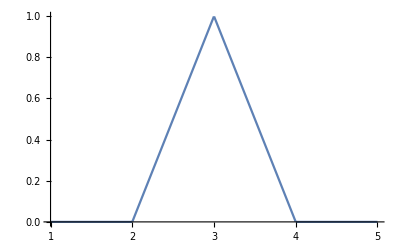

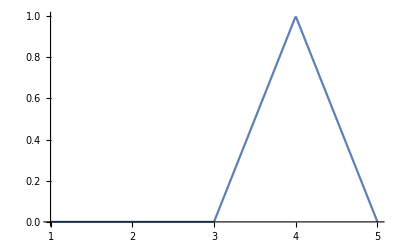

```mathematica
Remove["Global`*"]
data = {1,2,3,4,5}
(*data = {{1,1},{2,3},{3,2},,{4,4},{5,2}}*)
(*data[[1,1]] (*First pos in first point - PISEWISE*)*)


i = 2;
Do[
	Print[Plot[Piecewise[
	{{(x - data[[i-1]])/(data[[i]]-data[[i-1]]), data[[i-1]] < x < data[[i]]}, 
	{(data[[i+1]]-x)/(data[[i+1]]-data[[i]]), data[[i]] < x < data[[i+1]]}
	}], {x,1,5}]]	
,{i, 2, 4, 1}]
```

```mathematica
data[[i-1]]
```

Exercise 2.2
Estimate y at x = 4.2 using Linear interpolation

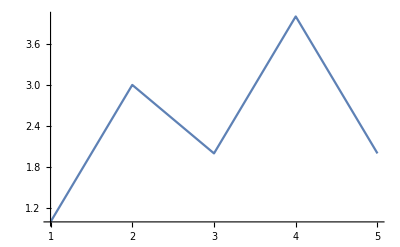

3.6

```mathematica
Remove["Global`*"]
xv = {1,2,3,4,5};
yv = {1,3,2,4,2};
data = Transpose[{xv,yv}];
f = Interpolation[yv, InterpolationOrder->1];
Plot[f[x],{x,1,5}]
f[4.2]
```

Exercise 2.3

1+(2+(-3/2+(1-13/24 (-4+x)) (-3+x)) (-2+x)) (-1+x)

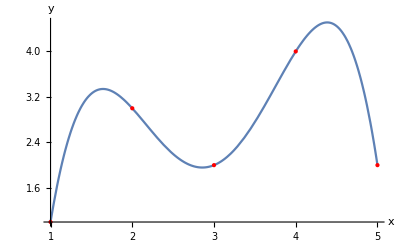

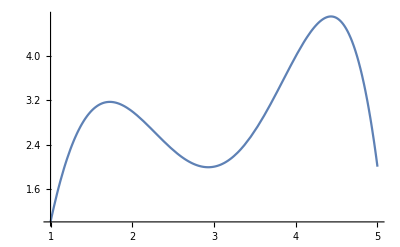

```mathematica
xv = {1,2,3,4,5};
yv = {1,3,2,4,2};
data = Transpose[{xv,yv}];

gd = ListPlot[data, PlotStyle->{Red, PointSize[Large]}, AxesLabel->{x, y}];

f = InterpolatingPolynomial[yv, x]
Show[Plot[f,{x,1,5}, AxesLabel->{x, y}], gd]

p = Fit[data,{1, x, x^2,x^4,x^5},x];
Show[Plot[p,{x, 1, 5}, AxesLabel->{x, y}], gd];

Plot[D[p],{x,1,5}]
```

Exercise 2.4